# ARMA

#### Model

X_t=c+ε_t+(∑_(i=1))^p φ_i X_(t-i)+(∑_(i=1))^q θ_i ε_(t-i)

```mathematica
RandomVariate[NormalDistribution[]]
```

-1.03055

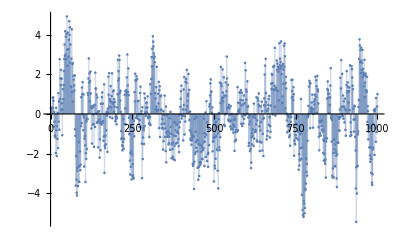

```mathematica
Block[{c=0.0,p=6,q=4,t=1000},
Block[{φs=Table[0.1,{i,p}],θs=Table[0.4,{i,q}],
X=Table[0.15,{i,t}],ε=Table[RandomVariate[NormalDistribution[]],{i,t}]},
Do[X[[i]]=0.3,{i,p}];
Do[X[[n+p]]=c+ε[[n+p]]
+Sum[X[[n+p-i]]φs[[i]],{i,p}]
+Sum[ε[[n+p-i]]θs[[i]],{i,q}],{n,t-p}];
ListPlot[X,Filling->Axis]
]]
```

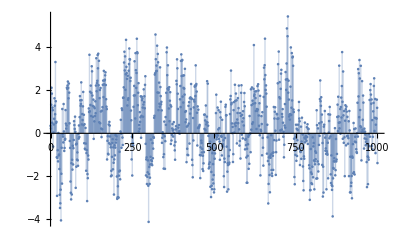

```mathematica
ListPlot[RandomFunction[ARMAProcess[0,Table[0.1,{i,6}],Table[0.4,{i,4}],1],{0,1000}],Filling->Axis]
```